# Physics through computational Thinking

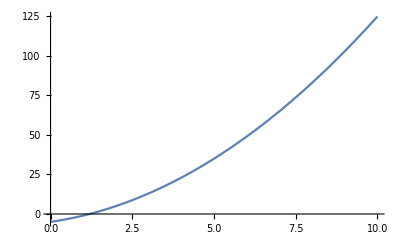

```mathematica
Plot[x^2+3 x-5,{x,0,10}]
```

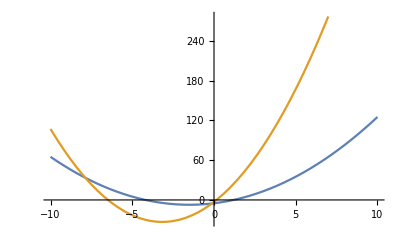

```mathematica
Plot[{x^2+3 x-5,3x^2+19x-3},{x,-10,10}]
```

```mathematica
ListPlot[Sin[x],{x,1,5}]
```

ListPlot::nonopt: Options expected (instead of {x,1,5}) beyond position 1 in ListPlot[Sin[x],{x,1,5}]. An option must be a rule or a list of rules.

ListPlot[Sin[x],{x,1,5}]

```mathematica
List[1,10]
```

{1,10}

```mathematica
Table[x,{x,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Numbers=Table[n,{n,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

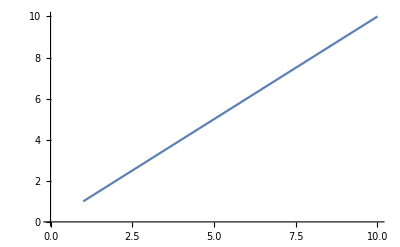

```mathematica
ListPlot[Numbers ,Joined->True]
```

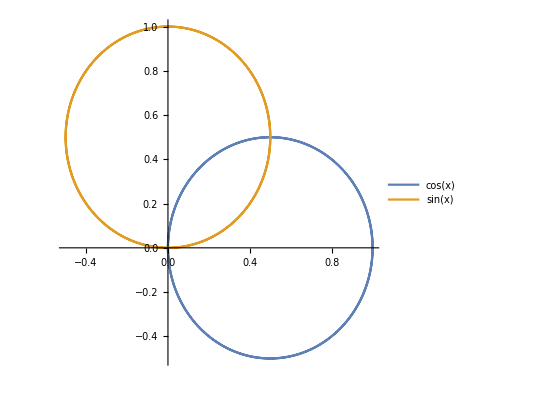

```mathematica
PolarPlot[{Cos[x],Sin[x]},{x,0,2 Pi},PlotLegends->"Expressions"]
```

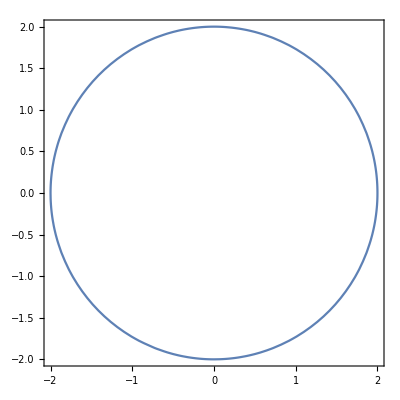

```mathematica
ContourPlot[x^2 +y^2==4,{x,-2,2},{y,-2,2}]
```

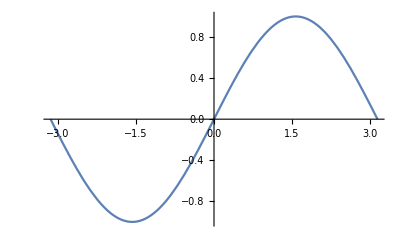

```mathematica
Plot[Sin[x],{x,-Pi,Pi}]
```

```mathematica
Table[Plot[Sin[n x],{x,-Pi,Pi}],{n,1,5}]
```

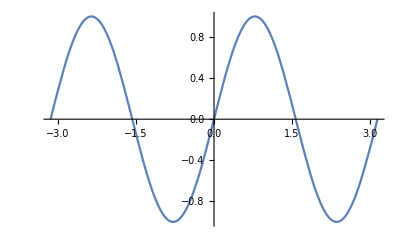
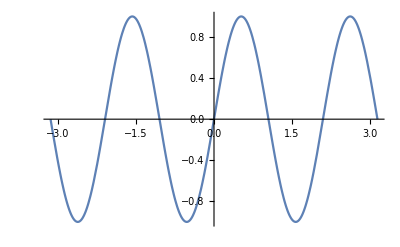
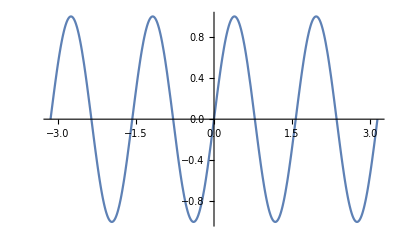
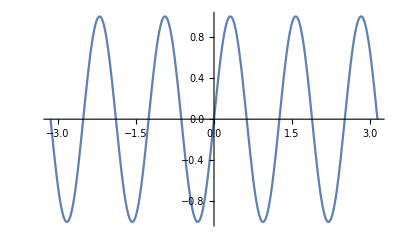
```mathematica
{-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-}
```

```mathematica
Manipulate[Plot[a x^2+b x+c,{x,-10,10}],{a,-10,10},{b,-10,10},{c,0,50}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,50},Frame->True]
```